```mathematica
dim=8;
Clear[μ,η]
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}];
```

```mathematica
SBT
```

{B[0]→2 A[0]+Log[(η μ A[1]^2 A[3] A[5])/(√((η μ A[1]^2+A[5]) (η A[1]^2+μ A[5])) ((μ A[3]^2+η A[1]^2 A[5]) (A[3]^2+η μ A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]) (1+η μ A[1]^2 A[3]^2 A[5]))^(1/4))],B[1]→(A[1] A[2] √(μ A[3]^4+η A[1]^2 A[3]^2 A[5]+η μ^2 A[1]^2 A[3]^2 A[5]+η^2 μ A[1]^4 A[5]^2))/(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))^(1/4),B[2]→1/(√((η μ A[1]^2+A[5])/(η A[1]^2+μ A[5])) (((A[3]^2+η μ A[1]^2 A[5]) (1+η μ A[1]^2 A[3]^2 A[5]))/(μ^2 A[3]^2+η μ A[1]^2 (1+A[3]^4) A[5]+η^2 A[1]^4 A[3]^2 A[5]^2))^(1/4)),B[3]→A[3] A[4] √((η^2 μ A[1]^4+η A[1]^2 A[5]+η μ^2 A[1]^2 A[5]+μ A[5]^2)/(μ A[3]^2+η A[1]^2 A[5]+η μ^2 A[1]^2 A[3]^4 A[5]+η^2 μ A[1]^4 A[3]^2 A[5]^2)),B[4]→((A[3]^2+η μ A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/(√(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2))),B[5]→((η μ A[1]^2+A[5]) (μ A[3]^2+η A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/((η A[1]^2+μ A[5]) √(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2)))}

```mathematica
f[3]= A[3] A[4] √((η^2 μ A[1]^4+η A[1]^2 A[5]+η μ^2 A[1]^2 A[5]+μ A[5]^2)/(μ A[3]^2+η A[1]^2 A[5]+η μ^2 A[1]^2 A[3]^4 A[5]+η^2 μ A[1]^4 A[3]^2 A[5]^2));
f[4]=((A[3]^2+η μ A[1]^2 A[5]) (μ+η A[1]^2 A[3]^2 A[5]))/(√(η^2 A[1]^4 A[3]^4 A[5]^2+η^2 μ^4 A[1]^4 A[3]^4 A[5]^2+η μ A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+η μ^3 A[1]^2 A[3]^2 (1+A[3]^4) A[5] (1+η^2 A[1]^4 A[5]^2)+μ^2 (η^2 A[1]^4 A[5]^2+η^2 A[1]^4 A[3]^8 A[5]^2+A[3]^4 (1+η^2 A[1]^4 A[5]^2)^2)));
```

```mathematica
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
```

```mathematica
κλ=ConstantArray[0,{128,2}];
μ=0.01;
η=1;
InitRG;
For[kind=1,kind<12,++kind,
RG;
Part[Part[κλ,kind],1]=f[3]/.SAT;
Part[Part[κλ,kind],2]=f[4]/.SAT;
]
```

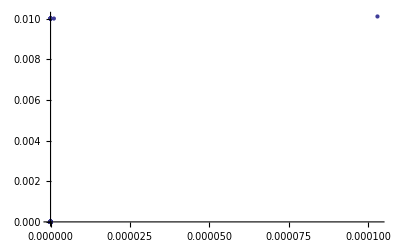

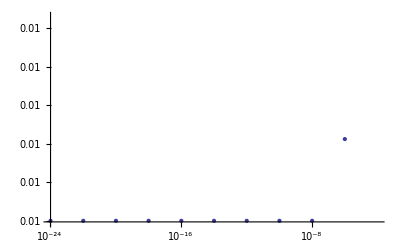

```mathematica
ListPlot[κλ,PlotStyle->Thick,AxesOrigin->{0,0}]
ListLogLogPlot[κλ,PlotStyle->Thick]
```

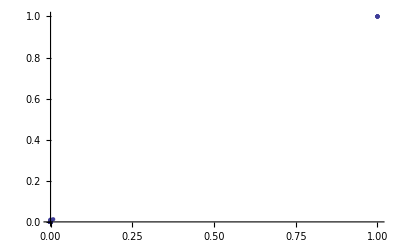

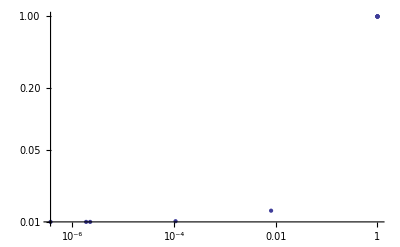

```mathematica
κλ=ConstantArray[0,{128,2}];
μ=0.01;
η=Exp[-2*0.1];
InitRG;
For[kind=1,kind<12,++kind,
RG;
Part[Part[κλ,kind],1]=f[3]/.SAT;
Part[Part[κλ,kind],2]=f[4]/.SAT;
]
ListPlot[κλ,PlotStyle->Thick,AxesOrigin->{0,0}]
ListLogLogPlot[κλ,PlotStyle->Thick]
```

```mathematica
κλ=ConstantArray[0,{3,128,2}];
μ=0.01;
ηvector={0.001,0.01,0.1};
η=Exp[-2*0.1];
For[i=1,i<3,++i,
η=Exp[-2*Part[ηvector,i]];
InitRG;
For[kind=1,kind<12,++kind,
RG;
Part[Part[Part[κλ,i],kind],1]=f[3]/.SAT;
Part[Part[Part[κλ,i],kind],1]=f[4]/.SAT;;
]
]
```

ReplaceAll::reps: {{A[0] → -6.92268, A[1] → 0.993054, A[2] → 0.997034, A[3] → 0.0101, A[4] → 0.0101, A[5] → 1.00584, 0.01 → 0.01, 0.998002 → 0.998002} ;; All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{A[0] → -20.7582, A[1] → 0.985162, A[2] → 0.98934, A[3] → 0.00010303, A[4] → 0.010102, A[5] → 1.02146, 0.01 → 0.01, 0.998002 → 0.998002} ;; All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{A[0] → -53.0094, A[1] → 0.969476, A[2] → 0.974299, A[3] → 1.05123×10^-6, A[4] → 0.01, A[5] → 1.05345, 0.01 → 0.01, 0.998002 → 0.998002} ;; All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
ListPlot[Part[κλ],PlotStyle->Thick,AxesOrigin->{0,0}]
ListLogLogPlot[κλ,PlotStyle->Thick]
```

{0.001,0.01,0.1}